

```mathematica
pt=Plot[Sin[x],{x,0,2 Pi}]
```

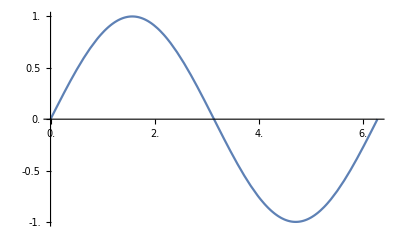

```mathematica
c=10;(*scale factor*)tx=Map[MapAt[c #&,#,3]&,Ticks/.AbsoluteOptions[pt,Ticks],{2}];
Show[pt,Ticks->tx]
```